```mathematica
f[x_,sigma_]:=Exp[-x^2/2*sigma^2]
```

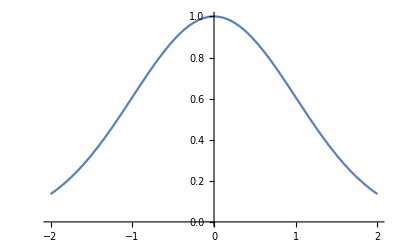

```mathematica
Plot[f[x,1],{x,-2,2}]
```

```mathematica
testval=Table[0.1*i,{i,-500,500}];
```

```mathematica
f[#,1]&/@testval;
```

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1245.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1240.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1245.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1240.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

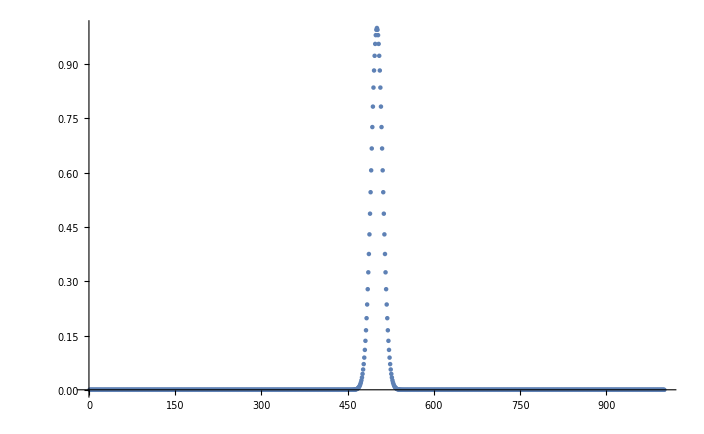

```mathematica
ListPlot[f[#,1]&/@testval,PlotRange->Full]
```

```mathematica
discreteseq=f[#,1]&/@testval;
```

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1245.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1240.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
vis=Abs[Fourier[discreteseq]]^2;
```

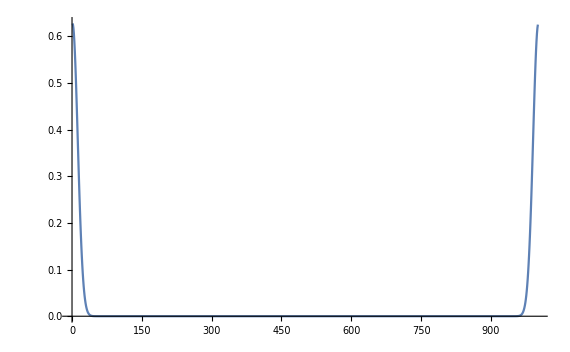

```mathematica
ListPlot[vis,Joined->True,PlotRange->Full]
```

```mathematica
inttest=Import["/Users/danielegana/Dropbox (PI)/ML/code/AGN/agndisk/agndisk/files/outputint/intensityfile","Table"];
```

```mathematica
Dimensions[inttest]
```

{128,128}

```mathematica
ListDensityPlot[inttest]
```

-Graphics-

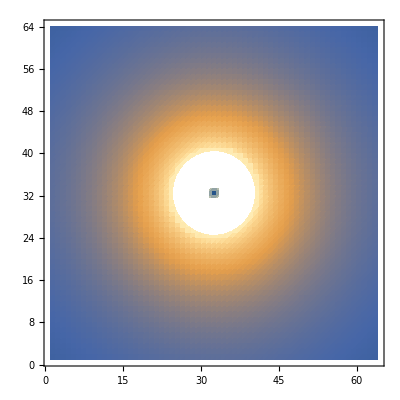

```mathematica
ListDensityPlot[inttest]
```

```mathematica
Quit[]
```

```mathematica
Needs["FourierSeries`"]
```

```mathematica
testfun=InverseFourierTransform[Exp[I*k^3],k,x]
```

(π (x+Abs[x]) AiryAi[-Abs[x]/3^(1/3)]+π (-x+Abs[x]) AiryAi[Abs[x]/3^(1/3)])/(3^(1/3) √(2 π) Abs[x])

```mathematica
Clear[testfun,testfun0]
```

```mathematica
testfun[x_]:=NInverseFourierTransform[Exp[I*k^3]*Exp[-k^2],k,x]
testfun0[x_]:=NInverseFourierTransform[Exp[-k^2],k,x]
```

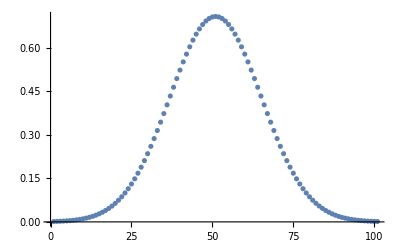

```mathematica
ListPlot[Table[testfun0[0.1*i],{i,-50,50}]]
```

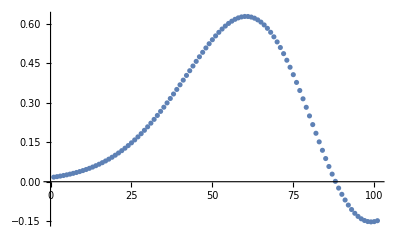

```mathematica
ListPlot[Table[testfun[0.1*i],{i,-50,50}]]
```

```mathematica
Plot[testfun/.x->z,{z,-10,10}]
```

$Aborted

```mathematica
NInverseFourierTransform[(ω^2+3 ω+5)*E^(-ω^2+1),ω,3.7]
```

NInverseFourierTransform[ⅇ^(1-ω^2) (5+3 ω+ω^2),ω,3.7]

```mathematica
InverseFourierTransform[Exp[I*k^3],k,x]/.x->10//N
```

0.226863

```mathematica
vis=Abs[Fourier[inttest]]^2;
```

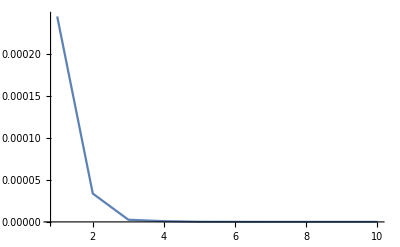

```mathematica
ListPlot[vis[[1;;10,1]],PlotRange->All,Joined->True]
```

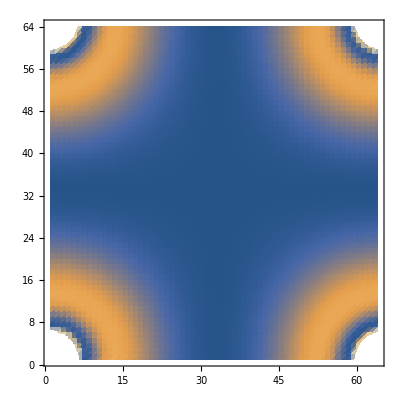

```mathematica
ListDensityPlot[vis]
```

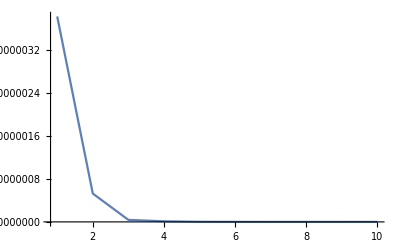

```mathematica
ListPlot[vis[[1;;10,1]],PlotRange->All,Joined->True]
```

```mathematica
ListDensityPlot[vis]
```

-Graphics-

```mathematica
2^6
```

64

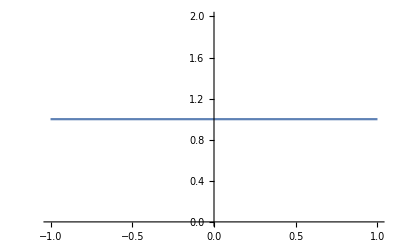

```mathematica
Plot[HeavisidePi[x/2],{x,-1,1} ]
```

```mathematica
len=10;
```

```mathematica
numsamples=50;
```

```mathematica
xsamples=N[Table[len/(numsamples/2)*n+0.00001,{n,-numsamples/2,numsamples/2}]];
```

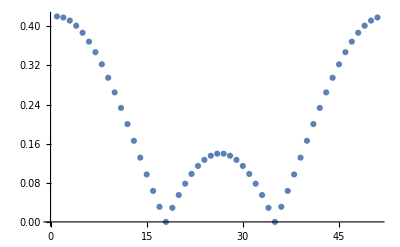

```mathematica
ListPlot[Abs[Fourier[HeavisidePi[#]&/@xsamples]],PlotRange->All]
```

```mathematica
numsamples=200;
```

```mathematica
xsamples=N[Table[len/(numsamples/2)*n+0.00001,{n,-numsamples/2,numsamples/2}]];
```

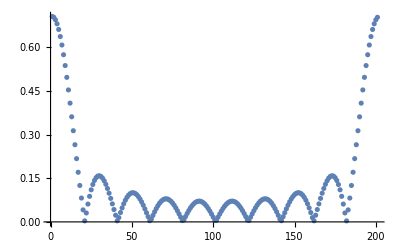

```mathematica
ListPlot[Abs[Fourier[HeavisidePi[#]&/@xsamples]],PlotRange->All]
```